```mathematica
Clear[k,r,a,b]
```

```mathematica
?r
```

logisticRegression`r

```mathematica
Get["logisticRegression`"]
```

r::shdw: Symbol r appears in multiple contexts {logisticRegression`,cephalon`}; definitions in context logisticRegression` may shadow or be shadowed by other definitions.

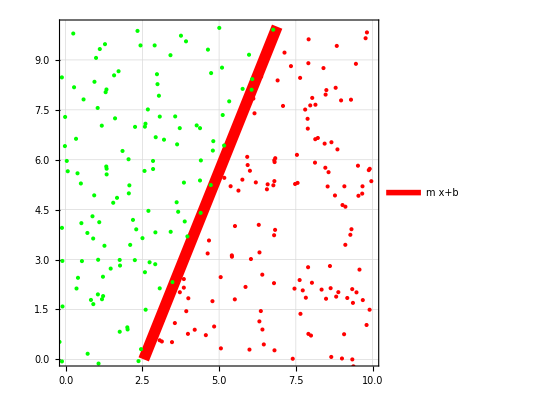
-Graphics--Graphics-

```mathematica
m=2.3;b=-5.85;
left=Cases[square,{x_,y_}/; m x+b<y];
right=Complement[square,left];
data3=((#->0)&/@left)~Join~((#->1)&/@right);
f=Classify[data3,TargetDevice->"GPU"];
Overlay[{
underneath=Rotate[ArrayPlot[Table[f[{x,y}],{x,0,10},{y,0,10}],Frame->False,ColorRules->{0->Gray,1->White}],π/2],
Show[Plot[m x+b,{x,0,10},PlotRange->{{0,10},{0,10}},PlotTheme->"Detailed",PlotStyle->{Red,Thickness[.02]},AspectRatio->1],
ListPlot[left,PlotStyle->Green,AspectRatio->1],
ListPlot[right,PlotStyle->Red,AspectRatio->1]]
}
]
```

```mathematica
S
```